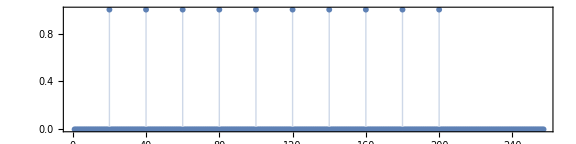

```mathematica
sr=512;
ts=1/sr;
harmonics=Table[20x,{x,0,10}];
inharmonics={33,123,87,5,101,181,199};
hData = Table[{t,Sum[Sin[2Pi fr t] ,{fr,harmonics}]//N},{t,0,1-ts,ts}];
inhData = Table[{t,Sum[Sin[2Pi fr t],{fr,inharmonics}]//N},{t,0,1-ts,ts}];
DiscreteSpectrum[data_]:=Module[{scale,half,len},
len=Length@data;
scale=1/Sqrt[len/4];
half=If[EvenQ[len],Floor[len/2],Floor[len/2]+1];
scale Abs@Reverse@Fourier[data[[All,2]]][[half;;]]
];
ds=DiscreteSpectrum[hData];
ListPlot[ds,PlotRange->All,Filling->Bottom,AspectRatio->1/4,ImageSize->Large,Frame->True,FrameTicks->{{Automatic,None}, {Automatic,harmonics}}]
```

```mathematica
+
```